Solution to general 4 state model with forward k rates and reverse r rates

```mathematica
ass={ koff>0 , km>0, kp>0, kon>0, koff0<koff1, koff0>0, koff1>0, b > 1};
```

```mathematica
sys={k1 p1 - r1 p2, k2 p2 - r2 p3, k3 p3 - r3 p4, k4 p4 - r4 p1, p1+p2+p3+p4}
```

{k1 p1-p2 r1,k2 p2-p3 r2,k3 p3-p4 r3,k4 p4-p1 r4,p1+p2+p3+p4}

```mathematica
sys = sys/.{k1-> kon, k2->  kon,k3-> km, k4-> b km,r1-> koff, r2-> koff, r3->  kp, r4->   kp};
sys = sys /. {km-> 1,kp -> kon /koff} (* nondim to km and enforce equilibrium*)
```

{kon p1-koff p2,kon p2-koff p3,p3-(kon p4)/koff,-(kon p1)/koff+b p4,p1+p2+p3+p4}

```mathematica
sol = FullSimplify[Solve[{J,J,J,J,1}==sys, {J, p1,p2,p3,p4}]]
```

{{J→((-1+b) koff^2 kon^2)/(b koff^3 (1+koff)+koff^2 (1+2 koff+b (2+koff)) kon+koff (3+(2+b) koff) kon^2+(1+koff) kon^3),p1→(koff^2 (koff kon+b (koff+koff^2+kon)))/(b koff^3 (1+koff)+koff^2 (1+2 koff+b (2+koff)) kon+koff (3+(2+b) koff) kon^2+(1+koff) kon^3),p2→(koff (1+koff) kon (b koff+kon))/(b koff^3 (1+koff)+koff^2 (1+2 koff+b (2+koff)) kon+koff (3+(2+b) koff) kon^2+(1+koff) kon^3),p3→(kon^2 (kon+koff (1+b koff+kon)))/(b koff^3 (1+koff)+koff^2 (1+2 koff+b (2+koff)) kon+koff (3+(2+b) koff) kon^2+(1+koff) kon^3),p4→(koff (1+koff) kon (koff+kon))/(b koff^3 (1+koff)+koff^2 (1+2 koff+b (2+koff)) kon+koff (3+(2+b) koff) kon^2+(1+koff) kon^3)}}

We are treating state 3 as the productive state - i.e. the one in which transcription happens.

```mathematica
p3cb[kon_] = p3/. sol[[1]]
```

(kon^2 (kon+koff (1+b koff+kon)))/(b koff^3 (1+koff)+koff^2 (1+2 koff+b (2+koff)) kon+koff (3+(2+b) koff) kon^2+(1+koff) kon^3)

```mathematica
p3c[kon_] = FullSimplify[p3cb[kon] /. {b -> 1}]
```

kon^2/(koff+kon)^2

```mathematica
p3cb[kon]
```

(kon^2 (kon+koff (1+b koff+kon)))/(b koff^3 (1+koff)+koff^2 (1+2 koff+b (2+koff)) kon+koff (3+(2+b) koff) kon^2+(1+koff) kon^3)

#### Calculate fidelity ratios in/out of equilibrium

```mathematica
eqRatio = p3c[kon*c] /p3c[kon]
noneqRatio = FullSimplify[p3cb[kon*c ] / p3cb[kon]]
```

(c^2 (koff+kon)^2)/(koff+c kon)^2

(c^2 (koff+b koff^2+c kon+c koff kon) (b koff^3 (1+koff)+koff^2 (1+2 koff+b (2+koff)) kon+koff (3+(2+b) koff) kon^2+(1+koff) kon^3))/((b koff^3 (1+koff)+c koff^2 (1+2 koff+b (2+koff)) kon+c^2 koff (3+(2+b) koff) kon^2+c^3 (1+koff) kon^3) (kon+koff (1+b koff+kon)))

### Find optimum

```mathematica
fidelityInfBeta = Limit[noneqRatio , b->Infinity]
```

(c^2 koff^5+c^2 koff^6+2 c^2 koff^4 kon+c^2 koff^5 kon+c^2 koff^4 kon^2)/(koff^5+koff^6+2 c koff^4 kon+c koff^5 kon+c^2 koff^4 kon^2)

```mathematica
fidelityInfKoff = Limit[fidelityInfBeta , koff->Infinity]
```

c^2

```mathematica
concRatio= noneqRatio/. {kp-> 1, kon-> 1, c-> 10};
concRatio = FullSimplify[concRatio]
```

(100 (10+koff (11+b koff)) (1+koff (4+koff (3+2 koff+b (3+koff (2+koff))))))/((1+koff (2+b koff)) (1000+koff (1300+koff (210+20 koff+b (120+koff (11+koff))))))

```mathematica
Limit[concRatio,b->Infinity]
```

(300 koff^4+200 koff^5+100 koff^6)/(120 koff^4+11 koff^5+koff^6)

```mathematica
concFunction[koff_,b_] = concRatio /100;
```

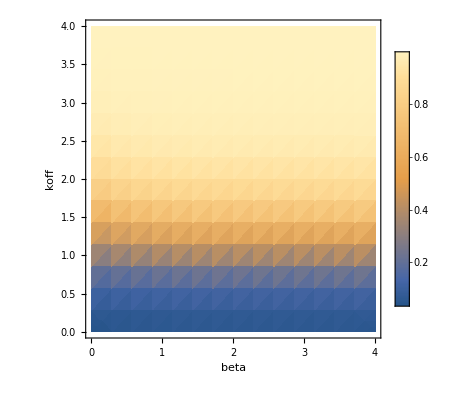

```mathematica
DensityPlot[concFunction[koff,b],{b,1,10^4},{koff,1,10^4},FrameLabel->{"beta","koff"},PlotLegends->Automatic, ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
errorRate[koff_,b_] = .5*( p3cb[koff]*(1/concRatio - 1) + 1) /. {kon->1,kp->1}
```

0.5 (1+(koff^2 (koff+koff (1+koff+b koff)) (-1+((1+koff (2+b koff)) (1000+koff (1300+koff (210+20 koff+b (120+koff (11+koff))))))/(100 (10+koff (11+b koff)) (1+koff (4+koff (3+2 koff+b (3+koff (2+koff))))))))/(koff^3 (1+koff)+b koff^3 (1+koff)+koff^3 (3+(2+b) koff)+koff^3 (1+2 koff+b (2+koff))))

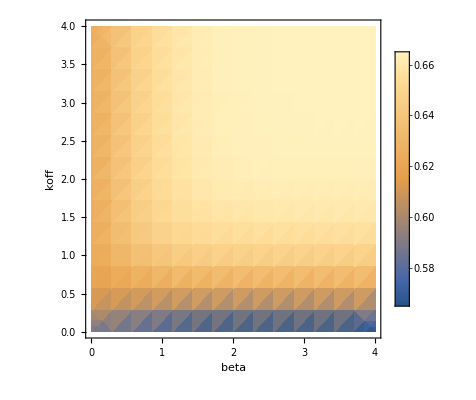

```mathematica
DensityPlot[1-errorRate[koff,b],{b,1,10^4},{koff,1,10^4},FrameLabel->{"beta","koff"},PlotLegends->Automatic,PlotRange->All,ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
N[p3cb[1] /. {b->10,kp-> 1,kon->1}]
```

(1.+koff (2.+10. koff))/(1.+koff+10. koff^3 (1.+koff)+koff (3.+12. koff)+koff^2 (1.+2. koff+10. (2.+koff)))

```mathematica
1 - errorRate[1000000,1]
```

0.62375

```mathematica
N[concFunction[1000000,1]]
```

0.999982